```mathematica
Solve[Cos[x] == -1/Sqrt[2] &&x>0 && x < Pi, x]
```

{{x→(3 π)/4}}

```mathematica
Solve[-10 == rho*Cos[phi] && 10 == rho*Sin[phi]*Sin[theta] && -10 == rho*Sin[phi]*Cos[theta] && rho>0 && phi > 0 && phi < Pi && theta > 0 && theta < 2*Pi, {rho,phi,theta}]
```

{{rho→10 √3,phi→2 ArcTan[√((1+√3)/(-1+√3))],theta→(3 π)/4}}

```mathematica
(ArcCos[-1/Sqrt[3]] - 2*ArcTan[Sqrt[(1+Sqrt[3])/(-1+Sqrt[3])]])//N
```

0.

```mathematica
Integrate[Integrate[Integrate[rho*Cos[phi]*rho^2*Sin[phi], {rho, 0, 1}],{theta, 0, 2*Pi}],{phi, 0,Pi/2}]
```

π/4

```mathematica
V = Integrate[Integrate[Integrate[rho^2*Sin[phi], {rho, 0, 1}],{theta, 0, 2*Pi}],{phi, 0,Pi/2}]
```

(2 π)/3

```mathematica
1/V*Integrate[Integrate[Integrate[rho^3*Sin[phi], {rho, 0, 1}],{theta, 0, 2*Pi}],{phi, 0,Pi/2}]
```

3/4

```mathematica
m =Integrate[Integrate[Sin[theta], {r, 1, 3}],{theta, 0, Pi}]
```

4

```mathematica
Integrate[Integrate[r*Cos[theta]*Sin[theta]/m, {r, 1, 3}],{theta, 0, Pi}]
```

0

```mathematica
f[r_]:=5*r;
```

```mathematica
f'[5]
```

5

```mathematica
g:=f[Sqrt[x^2+y^2]]
D[D[g,x],x]+D[D[g,y],y] // Simplify
```

5/(√(x^2+y^2))

```mathematica
Integrate[Integrate[2*r, {r, 0, 5}], {theta, 0, 2*Pi}]
```

50 π

```mathematica
Integrate[Integrate[(5)/(r)*r, {r, 0, 5}], {theta, 0, 2*Pi}]
```

50 π

```mathematica
Solve[{y==1/x && y == Sqrt[x^2-6]}, {x,y}]
```

{{x→-ⅈ √(-3+√10),y→ⅈ (3 √(-3+√10)+√(10 (-3+√10)))},{x→√(3+√10),y→-3 √(3+√10)+√(10 (3+√10))}}

```mathematica
x1=Sqrt[3+Sqrt[10]];
y1=-3*Sqrt[3+Sqrt[10]]+Sqrt[10*(3+Sqrt[10])];
```

```mathematica
x1 // N
y1//N
```

2.48239

0.402837

```mathematica
Solve[{y==2/x && y == Sqrt[x^2-6]}, {x,y}]
```

{{x→-ⅈ √(-3+√13),y→1/2 ⅈ (3 √(-3+√13)+√(13 (-3+√13)))},{x→√(3+√13),y→1/2 (-3 √(3+√13)+√(13 (3+√13)))}}

```mathematica
x2=Sqrt[3+Sqrt[13]];
y2=1/2*(-3*Sqrt[3+Sqrt[13]]+Sqrt[13*(3+Sqrt[13])]);
```

```mathematica
x2 // N
y2//N
```

2.57013

0.778172

```mathematica
Solve[{y==2/x && y == Sqrt[x^2-1]}, {x,y}]
```

{{x→-ⅈ √(1/2 (-1+√17)),y→1/8 ⅈ (√(2 (-1+√17))+√(34 (-1+√17)))},{x→√(1/2 (1+√17)),y→1/8 (-√(2 (1+√17))+√(34 (1+√17)))}}

```mathematica
x3=Sqrt[1/2*(1+Sqrt[17])];
y3=1/8*(-Sqrt[2*(1+Sqrt[17])]+Sqrt[34*(1+Sqrt[17])]);
```

```mathematica
x3 // N
y3//N
```

1.60049

1.24962

```mathematica
Solve[{y==1/x && y == Sqrt[x^2-1]}, {x,y}]
```

{{x→-ⅈ √(1/2 (-1+√5)),y→1/4 ⅈ (√(2 (-1+√5))+√(10 (-1+√5)))},{x→√(1/2 (1+√5)),y→1/4 (-√(2 (1+√5))+√(10 (1+√5)))}}

```mathematica
x4=Sqrt[1/2*(1+Sqrt[5])];
y4=1/4*(-Sqrt[2*(1+Sqrt[5])]+Sqrt[10*(1+Sqrt[5])]);
```

```mathematica
x4 // N
y4//N
```

1.27202

0.786151

```mathematica
fff[x_,y_,z_] := (2*x*z)/y+y/x;
yy1=Sqrt[x^2-1];
yy2=Sqrt[x^2-6];
yy3=2/x;
yy4=1/x;
```

```mathematica
i0 = Integrate[Integrate[Integrate[fff[x,y,z],{y,yy4,yy1}],{x, x4,x3}], {z,0,1}]+Integrate[Integrate[Integrate[fff[x,y,z],{y,yy4,yy3}],{x, x3,x1}], {z,0,1}]+Integrate[Integrate[Integrate[fff[x,y,z],{y,yy2,yy3}],{x, x1,x2}], {z,0,1}] // Simplify
```

1/32 (-4 (-1+√5) ArcCsch[2]+(-1+√5) Log[16]-2 √17 Log[256]+4 Log[-1+√5]-4 √5 Log[-1+√5]+48 Log[-3+√13]+48 Log[3+√13]-4 Log[-1+√17]+4 √17 Log[-1+√17]-4 Log[1+√17]+4 √17 Log[1+√17])

```mathematica
i0 // N
```

1.73287

```mathematica
limPos[a_] := a/2+Sqrt[a^2+4*v^2]/2;
fun = 2*z*u/v+v/u;
i1=Integrate[Integrate[Integrate[fun/(2*u), {u,limPos[1], limPos[6]}], {v,1,2}],{z,0,1}]//Simplify
i1 // N
```

Log[4 √2]

1.73287

```mathematica
Integrate[Integrate[1,{x,2*y-2,2-2*y}],{y,0,1}]
```

2

```mathematica
Integrate[Integrate[1/(3*u),{u,5,1}],{v,2,4}]
```

-(2 Log[5])/3

```mathematica
Integrate[Integrate[3*r,{r,0,1}],{t,0,2*Pi}]
```

3 π

```mathematica
Integrate[(5*Cos[t]+3*Sin[t])*(-Sin[t])+(1+Cos[Sin[t]])*Cos[t],{t,0,2*Pi}]
```

-3 π

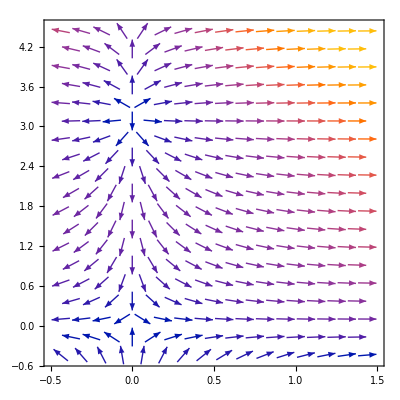

```mathematica
VectorPlot[{x*y+Sin[x]*Cos[y], -Cos[x]*Sin[y]},{x,-0.5, 1.5}, {y,-0.5, 4.5}]
```